## Solution of Schrodinger’s equation with modulated Gaussian initial value

Katharine Long, Texas Tech University

### Define the initial value

```mathematica
Subscript[ψ, 0][x_]=Exp[-x^2/(2a^2)]/Sqrt[a Sqrt[Pi]]Exp[I p x/ℏ]
```

(ⅇ^(-x^2/(2 a^2)+(ⅈ p x)/ℏ))/(π^(1/4) √a)

Check normalization

```mathematica
Integrate[Subscript[ψ, 0][x]Conjugate[Subscript[ψ, 0][x]],{x,-Infinity,Infinity},Assumptions->{a>0,p∈Reals,ℏ>0}]
```

1

### Take FT of initial profile

```mathematica
Subscript[ψ̃, 0][k_]=FourierTransform[Subscript[ψ, 0][x],x,k,FourierParameters->{0,-1},Assumptions->{a>0,p∈Reals,ℏ>0}]
```

(ⅇ^(-(a^2 (p-k ℏ)^2)/(2 ℏ^2)))/(π^(1/4) √(1/a^2) √a)

### FT of solution is (ψ̃)_0(k)exp(-i ℏ k^2 t/(2m))

```mathematica
ψ̃[k_,t_]=Subscript[ψ̃, 0][k]Exp[-I ℏ k^2 t/(2m)]
```

(exp(-(a^2 (p-k ℏ)^2)/(2 ℏ^2)-(ⅈ k^2 t ℏ)/(2 m)))/(π^(1/4) √(1/a^2) √a)

### Compute IFT to obtain solution

```mathematica
ψ[x_,t_]=InverseFourierTransform[ψ̃[k,t],k,x,FourierParameters->{0,-1},Assumptions->{m>0,t∈Reals,a>0,ℏ>0,p∈Reals}]
```

(exp((-2 a^2 m p x+a^2 p^2 t-ⅈ m x^2 ℏ)/(-2 t ℏ^2+2 ⅈ a^2 m ℏ)))/(π^(1/4) √(1/a^2) √a √(a^2+(ⅈ t ℏ)/m))

### Form probability: P(x,t)=|ψ(x,t)|^2

```mathematica
P[x_,t_]=ComplexExpand[ψ[x,t]Conjugate[ψ[x,t]]]//FullSimplify
```

(√(a^2) ⅇ^(-(a^2 (p t-m x)^2)/(a^4 m^2+t^2 ℏ^2)))/(√π √(a^4+(t^2 ℏ^2)/m^2))

```mathematica
P[v_,x_,t_]=P[x,t]/.{m->1,a->1,ℏ->1,p->v}
```

(ⅇ^(-(t v-x)^2/(t^2+1)))/(√π √(t^2+1))

```mathematica
plot[v_,t_]:=Plot[P[v,x,t],{x,-4,20},PlotRange->{0,1/Sqrt[Pi]}]
```

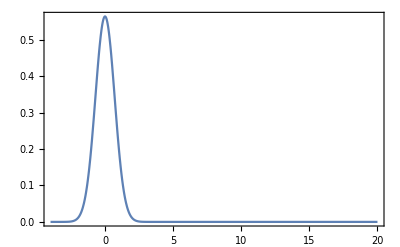

```mathematica
plot[3,0]
```

```mathematica
Manipulate[plot[10,t],{t,0,1}]
```